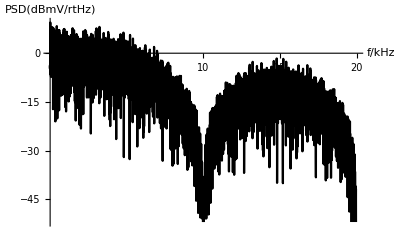

```mathematica
ts=0.0001;
tp=ts*4095;
tseq=Table[x,{x,0,tp-ts,ts}];
pnoi=Table[RandomReal[{-1,1}],{x,tseq}];
pnois=Table[pnoi[[Floor[x/4+1]]],{x,0,tp/ts*4-4}];
p=Periodogram[pnois,8192,8192,PlotStyle->{Black},AxesStyle->{{Black,10},{Black,10}},ScalingFunctions->"dB",SampleRate->40,AxesLabel->{"f/kHz","PSD(dBmV/rtHz)"}]
```

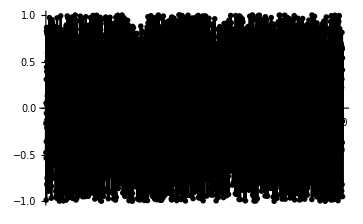

```mathematica
ListLinePlot[pnoi,PlotTheme->"Monochrome"]
```